```mathematica
ClearAll["Global`*"]
```

# SDPB Tutorial - 1

## Maximization with Constraints

Problem

Maximize { a, b } . { 0, -1 } = a × 0 + b × (-1) = -b over { a, b } such that:

{ a, b } . { 1, 0 } = a × 1 + b × 0 = a = 1

a × ( 1 + x^4) + b × (x^4/12 + x^2) ≥ 0

Analytical Solution

```mathematica
(* Function to maximize *)
f[x_,a_,b_]:=a*(1+x^4)+b*(x^4/12+x^2);
g[x_,b_]:=f[x,1,b];
g[x,b]
```

1+x^4+b (x^2+x^4/12)

```mathematica
(* Find the minimum in x and solve for b *)
MinTmp=Solve[D[g[x,b],x]==0,b]
```

{{b→-(12 x^2)/(6+x^2)}}

```mathematica
(* Plug the solution back into the expression *)
h[x_]:=FullSimplify[g[x,b]/.MinTmp[[1]]];
h[x]
```

(6+x^2-6 x^4)/(6+x^2)

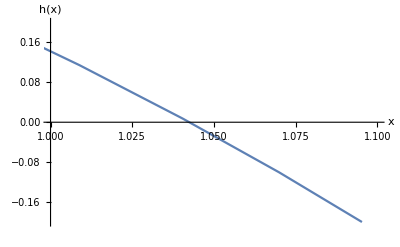

```mathematica
(* Plot the function *)
Plot[h[x],{x,0,1.5},AxesLabel->{"x","h(x)"},PlotRange->{{1.0,1.1},{-0.2,0.2}}]
```

```mathematica
(* Solve the positivity constraint *)
PositivityConstraint=FindRoot[h[x],{x,1.04},WorkingPrecision->15]
```

{x→1.04249678571816}

```mathematica
(* Find b_min *)
bMin=MinTmp/.PositivityConstraint
```

{{b→-1.840265763132}}

Discretized Solution

```mathematica
(* Consider a range for the variable x and compute the constraint over it *)
RangeX=Join[Table[x,{x,0,2,0.001}],Table[x,{x,2,10,0.1}],Table[x,{x,10,100,1}]];
Constraints=Table[N[Exp[-x]*f[x,a,b]],{x,RangeX}];
Dimensions[RangeX]==Dimensions[Constraints]
```

True

```mathematica
(* Consider what we want to maximize *)
Maxim={0,-1};
Normaliz={1,0};
Mat={Coefficient[Constraints,a],-Coefficient[Constraints,b]}//Transpose; (* the - sign is due to Mathematica minimizing things instead of maximizing them *)
MatFull=Join[Mat,{Normaliz}];
BVecTotal=Join[Table[{0,1},Length[Constraints]],{{1,0}}];
```

```mathematica
(* Find vector X = {a,b} such that it maximizes Maxim . X such that MatFull . X ≥ BVecTotal and x ≥ 0 *)
Result=LinearProgramming[Maxim,MatFull,BVecTotal]
```

{1.,1.84027}

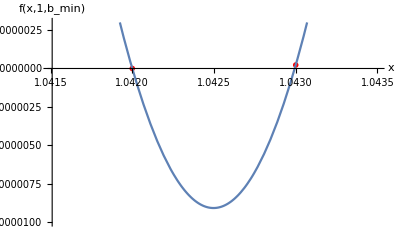

```mathematica
(* Test the solution: there is a region where the function is negative, but the computed points are positive. The algorithm works but it is not accurate everywhere. *)
minx=1.0415;
maxx=1.0435;
miny=-10^(-6);
maxy=3*10^(-7);
TestPoints=Table[{x,g[x,-Result[[2]]]},{x,RangeX}];
TestFunction[x_]:=g[x,-Result[[2]]];
TestList=ListPlot[TestPoints,PlotRange->{{minx,maxx},{miny,maxy}},PlotMarkers->{Automatic,Medium},PlotStyle->Red];
TestPlot=Plot[TestFunction[x],{x,minx,maxx},PlotRange->{{minx,maxx},{miny,maxy}}];
Show[TestList,TestPlot,PlotRange->{{minx,maxx},{miny,maxy}},AxesLabel->{"x","f(x,1,b_min)"}]
```

Solution Using SDPB

```mathematica
(* Invoke SDPB *)
<<"SDPB.m"
```

```mathematica
(* Locate the executable *)
SDPBexe="/usr/local/bin/sdpb";
```

```mathematica
(* Pass all the parameters to SDPB... *)
SDPB[datFile_]:= Module[
    {
    (*The prefactor DampedRational[1,{},1/E,x] does not affect the answer but it affects the choice of sample scalings and bilinear basis.*)
        pols = {PositiveMatrixWithPrefactor[DampedRational[1,{},1/E,x], {{{1 + x^4, x^4/12 + x^2}}}]}, (* list of polynomials *)
        norm = {1, 0}, (*normalization vector*)
        obj  = {0, -1} (*vector to maximize *)
    },
    WriteBootstrapSDP[datFile, SDP[obj, norm, pols]];]; 

(* ...and call the function *)
SDPB[InFile=FileNameJoin[{$HomeDirectory,"sdpb.in"}]];
```

```mathematica
(* Test the installation *)
TestSDPBInstall=StringJoin[SDPBexe," --help > ",FileNameJoin[{$HomeDirectory, "SDPBinstall.test"}]];
Run[TestSDPBInstall];
```

```mathematica
(* Now run the SDPB command for real *)
ParamFile=FileNameJoin[{$HomeDirectory,"param.sdpb"}];
SDPBCommand[in_,out_] := StringJoin[SDPBexe," -s ",in," -p ", ParamFile, " > ",out];
Run[SDPBCommand[InFile,FileNameJoin[{$HomeDirectory,"sdpb.out"}]]];
```